```mathematica
Quit[]
```

## Input

```mathematica
<<"/home/riccardo/Programs/FeynArts/FeynArts/FeynArts.m"
```

FeynArts 3.11 (25 Mar 2022)

by Hagen Eck, Sepp Kueblbeck, and Thomas Hahn

```mathematica
<<"/home/riccardo/Programs/FormCalc/FormCalc/FormCalc.m"
```

FormCalc 9.10 (30 Aug 2022)

by Thomas Hahn

```mathematica
Remove[q1]
Remove[q2]
<<"/home/riccardo/Programs/ABISS/ABISS.m"
```

+++++ ABISS` +++++
Version 1.0.0

Amplitudes Builder, Interference Solver and Simplifier

ABISS: A link to the model file SMbgf_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general_backup.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_FARAMIR_general+SM.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgfQCD_Anglerfish.mod has been added to the FeynArts directory

ABISS: A link to the model file SMbgf_TelescopeOctopus_backup.mod has been added to the FeynArts directory

```mathematica
SetPath[NotebookDirectory[]];
```

Define the process:

```mathematica
SetProcess[{V[30]}->{S[30]}];
```

Generate default Input files

```mathematica
GenerateInput[];
```

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m already exist. It will NOT be overwritten.

ABISS Warning: Input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m already exist. It will NOT be overwritten.

Import the input files (kinematics + integral families).

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m.

## Diagrams generation

Generate diagrams using feynarts (charged current drell-yan, one loop boxes and born).

```mathematica
SetOptions[InsertFields,  Model -> "SMbgf_Anglerfish", GenericModel ->"Lorentzbgf", InsertionLevel->{Particles}, Restrictions->{NoQuarkMixing}, ExcludeParticles-> {}];
```

```mathematica
process={V[30]}->{S[30]};
```

```mathematica
topologies1L=CreateTopologies[1,1-> 1,ExcludeTopologies->Tadpoles];
```

```mathematica
fields1L=InsertFields[topologies1L, process];
```

loading generic model file /home/riccardo/Programs/FeynArts/FeynArts/Models/Lorentzbgf.gen

> $GenericMixing is OFF

generic model {Lorentzbgf} initialized

loading classes model file /home/riccardo/Programs/FeynArts/FeynArts/Models/SMbgf_Anglerfish.mod

> 60 particles (incl. antiparticles) in 24 classes

> $CounterTerms are ON

> 689 vertices

> 334 counterterms of order 1

> 2 counterterms of order 2

classes model {SMbgf_Anglerfish} initialized

Excluding 24 field point(s) (incl. charge-conjugate ones)

inserting at level(s) {Particles}

> Top. 1: 0 Particles insertions

> Top. 2: 18 Particles insertions

Restoring 24 field point(s)

in total: 18 Particles insertions

```mathematica
amp1L=CreateFeynAmp[fields1L];
```

creating amplitudes at level(s) {Particles}

> Top. 1: 18 Particles amplitudes

in total: 18 Particles amplitudes

> Top. 1 ac/bd/cdcd.m, 0 diagrams

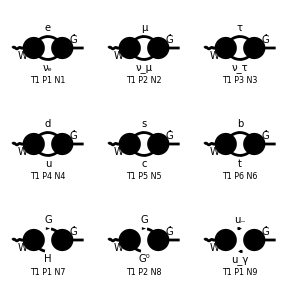

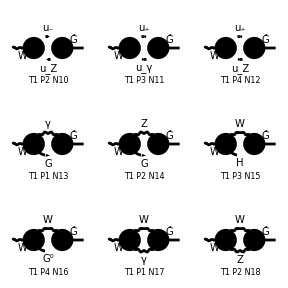

```mathematica
Paint[fields1L];
```

```mathematica
myAmp1L=ExtractAmplitude[amp1L];
```

```mathematica
SaveAmplitudes[myAmp1L,"OneLoopAmplitudes.m"];
```

ABISS: Amplitudes saved in /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/feynArts_amplitudes/OneLoopAmplitudes.m

## Projection and polarization vector

```mathematica
p[Lor1_]:=- I SP[p1,{Lor1}]/SP[p1,p1]
```

### Remove polarization vectors

```mathematica
removePolarizationVectors={PolarizationVector[V[30],p_,i_]->1}
```

{ep[V[30],p_,i_]→1}

## Interference

```mathematica
myAmp1LnoEP=myAmp1L/.removePolarizationVectors;
```

```mathematica
myAmp1LProjection=Map[#*p[Lor1]&,myAmp1LnoEP];
```

```mathematica
myAmp1LnoEP[[1]]
```

-1/(16 π^4)ⅈ FeynAmpDenominator[1/(q1)^2,1/(-ME^2+(q1-k1)^2)] tr[gs[-(q1)],-ⅈ EL gFll ME om_+,ME+gs[-(q1)+k1],ⅈ EL gWlN ga[Lor1].om_-]

```mathematica
myAmp1LProjection[[1]]
```

-1/(16 π^4 SP[p1,p1])FeynAmpDenominator[1/(q1)^2,1/(-ME^2+(q1-k1)^2)] tr[gs[-(q1)],-ⅈ EL gFll ME om_+,ME+gs[-(q1)+k1],ⅈ EL gWlN ga[Lor1].om_-] SP[p1,{Lor1}]

```mathematica
SquareSimplifyAndSave[myAmp1LProjection,{1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX//interferences/Contribution_18_1.m.

## Shift

```mathematica
ImportInput[];
```

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/integral_families.m.

ABISS: Imported input file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/input/kinematics.m.

```mathematica
Do[
ShiftAndSave[i,j,False];
,{i,18},{j,1}]
```

ABISS: Integral family {{E0, {ME}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_1_1.m.

ABISS: Integral family {{E0, {mm}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_2_1.m.

ABISS: Integral family {{E0, {ML}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_3_1.m.

ABISS: Integral family {{C0, {mu, md}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_4_1.m.

ABISS: Integral family {{C0, {MC, MS}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_5_1.m.

ABISS: Integral family {{C0, {MT, MB}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_6_1.m.

ABISS: Integral family {{C0, {MH, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_7_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_8_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_9_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_10_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_11_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_12_1.m.

ABISS: Integral family {{D0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_13_1.m.

ABISS: Integral family {{C0, {mw, mz}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_14_1.m.

ABISS: Integral family {{C0, {MH, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_15_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_16_1.m.

ABISS: Integral family {{E0, {mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_17_1.m.

ABISS: Integral family {{C0, {mz, mw}}} already recognised for /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/interferences/Contribution_18_1.m.

## KiraInput

```mathematica
Do[
GenerateAndSaveKiraInput[i,j];
,{i,18},{j,1}]
```

ABISS: Computed contribution 1-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_1_1.m.

ABISS: Computed contribution 2-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_2_1.m.

ABISS: Computed contribution 3-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_3_1.m.

ABISS: Computed contribution 4-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_4_1.m.

ABISS: Computed contribution 5-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_5_1.m.

ABISS: Computed contribution 6-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_6_1.m.

ABISS: Computed contribution 7-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_7_1.m.

ABISS: Computed contribution 8-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_8_1.m.

ABISS: Computed contribution 9-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_9_1.m.

ABISS: Computed contribution 10-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_10_1.m.

ABISS: Computed contribution 11-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_11_1.m.

ABISS: Computed contribution 12-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_12_1.m.

ABISS: Computed contribution 13-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_13_1.m.

ABISS: Computed contribution 14-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_14_1.m.

ABISS: Computed contribution 15-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_15_1.m.

ABISS: Computed contribution 16-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_16_1.m.

ABISS: Computed contribution 17-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_17_1.m.

ABISS: Computed contribution 18-1.

ABISS Warning: Overwritten file /home/riccardo/Documents/Tesi/TestABISS/SE_Test/WX/kira_input/Contribution_18_1.m.

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[E0,{ME},0,1],userIntegral[E0,{ME},1,0],userIntegral[E0,{ME},1,1],userIntegral[E0,{mm},0,1],userIntegral[E0,{mm},1,0],userIntegral[E0,{mm},1,1],userIntegral[E0,{ML},0,1],userIntegral[E0,{ML},1,0],userIntegral[E0,{ML},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[C0,{mu,md},1,0],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MC,MS},0,1],userIntegral[C0,{MC,MS},1,0],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MT,MB},0,1],userIntegral[C0,{MT,MB},1,0],userIntegral[C0,{MH,mw},1,1],userIntegral[C0,{MH,mw},0,1],userIntegral[C0,{MH,mw},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[C0,{mz,mw},1,0],userIntegral[E0,{mw},1,1],userIntegral[E0,{mw},0,1],userIntegral[E0,{mw},1,0],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
SaveScalarIntegrals["scalar_integrals"];
```

```mathematica
ExportScalarIntegrals["kira_scalar_integrals.dat"];
```

## Apply Kira sub;

```mathematica
ImportScalarIntegrals["scalar_integrals"];
```

```mathematica
ClearRules[]
```

{}

```mathematica
ImportRules[NotebookDirectory[]<>"kira_myintegrals.m"]
```

```mathematica
PrintRules[]
```

{userIntegral[E0,{m1},1,0]→0,userIntegral[E0,{m1},0,1]→userIntegral[B0,{m1},1,0],userIntegral[E0,{m1},1,1]→userIntegral[D0,{m1},1,1],userIntegral[C0,{m1,m2},1,0]→userIntegral[B0,{m1},1,0]}

```mathematica
PrintScalarIntegrals[]
```

{userIntegral[E0,{ME},0,1],userIntegral[E0,{ME},1,0],userIntegral[E0,{ME},1,1],userIntegral[E0,{mm},0,1],userIntegral[E0,{mm},1,0],userIntegral[E0,{mm},1,1],userIntegral[E0,{ML},0,1],userIntegral[E0,{ML},1,0],userIntegral[E0,{ML},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[C0,{mu,md},1,0],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MC,MS},0,1],userIntegral[C0,{MC,MS},1,0],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MT,MB},0,1],userIntegral[C0,{MT,MB},1,0],userIntegral[C0,{MH,mw},1,1],userIntegral[C0,{MH,mw},0,1],userIntegral[C0,{MH,mw},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[C0,{mz,mw},1,0],userIntegral[E0,{mw},1,1],userIntegral[E0,{mw},0,1],userIntegral[E0,{mw},1,0],userIntegral[D0,{mw},1,1],userIntegral[C0,{mw,mz},1,1]}

```mathematica
DetermineMasterIntegrals[]
```

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{ME},1,0],userIntegral[D0,{ME},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ML},1,0],userIntegral[D0,{ML},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MC,MS},0,1],userIntegral[B0,{MC},1,0],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MT,MB},0,1],userIntegral[B0,{MT},1,0],userIntegral[C0,{MH,mw},1,1],userIntegral[C0,{MH,mw},0,1],userIntegral[B0,{MH},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[B0,{mz},1,0],userIntegral[D0,{mw},1,1],userIntegral[B0,{mw},1,0],userIntegral[C0,{mw,mz},1,1]}

```mathematica
Do[
SaveResult[i,j];
,{i,18},{j,1}]
```

## Ward Identity Test

### Total coefficients

```mathematica
diagramCoefficients= {};
Do[diagramCoefficients=Append[diagramCoefficients,<<(NotebookDirectory[]<>"coefficients/Coefficients_"<>ToString[i]<>"_1.m")],{i,18}]
```

```mathematica
diagramCoefficients
```

{{(EL^2 gFll gWlN ME^2)/(16 π^4 psq),(EL^2 gFll gWlN (-ME^4+ME^2 psq))/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,(EL^2 gFll gWlN mm^2)/(16 π^4 psq),(EL^2 gFll gWlN (-mm^4+mm^2 psq))/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,(EL^2 gFll gWlN ML^2)/(16 π^4 psq),(EL^2 gFll gWlN (-ML^4+ML^2 psq))/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,(3 EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(8 π^4)+(3 EL^2 gFud gWdu md^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(3 EL^2 gFud gWdu mu^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq),(3 EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(3 EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(3 EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)+(3 EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(8 π^4)-(3 EL^2 gFud gWdu MC^2 (MC^2-MS^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(3 EL^2 gFud gWdu MS^2 (MC^2-MS^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq),-(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(3 EL^2 gFud gWdu MS^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)-(3 EL^2 gFud gWdu MS^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),0,0,0,0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(8 π^4)+(3 EL^2 gFud gWdu MB^2 (-MB^2+MT^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(3 EL^2 gFud gWdu MT^2 (-MB^2+MT^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq),(3 EL^2 gFud gWdu MB^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(3 EL^2 gFud gWdu MB^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)+(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),0,0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gHFF gHFW MH^2)/(16 π^4)-(EL^2 gHFF gHFW mw^2)/(16 π^4)-(EL^2 gHFF gHFW MH^2 (MH^2-mw^2+psq))/(16 π^4 psq)+(EL^2 gHFF gHFW mw^2 (MH^2-mw^2+psq))/(16 π^4 psq),-(EL^2 gHFF gHFW MH^2)/(16 π^4 psq)+(EL^2 gHFF gHFW mw^2)/(16 π^4 psq),(EL^2 gHFF gHFW MH^2)/(16 π^4 psq)-(EL^2 gHFF gHFW mw^2)/(16 π^4 psq),0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gXFF gXFW)/(16 π^4)+(EL^2 gXFF gXFW (-mw^2+mz^2+psq))/(16 π^4 psq),(EL^2 gXFF gXFW)/(16 π^4 psq),-(EL^2 gXFF gXFW)/(16 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gFgagm ggagmW)/(16 π^4)-(EL^2 gFgagm ggagmW (mw^2-psq))/(16 π^4 psq),(EL^2 gFgagm ggagmW)/(16 π^4 psq),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFgzgm ggzgmW sw)/(16 π^4)+(EL^2 gFgzgm ggzgmW (mw^2-mz^2-psq) sw)/(16 π^4 psq),-(EL^2 gFgzgm ggzgmW sw)/(16 π^4 psq),(EL^2 gFgzgm ggzgmW sw)/(16 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gFgagp ggagpW)/(16 π^4)-(EL^2 gFgagp ggagpW (mw^2-psq))/(16 π^4 psq),(EL^2 gFgagp ggagpW)/(16 π^4 psq),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFgzgp ggzgpW sw)/(16 π^4)+(EL^2 gFgzgp ggzgpW (mw^2-mz^2-psq) sw)/(16 π^4 psq),-(EL^2 gFgzgp ggzgpW sw)/(16 π^4 psq),(EL^2 gFgzgp ggzgpW sw)/(16 π^4 psq),0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,(EL^2 gFAW gFFA)/(4 π^4),0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(cw^2 EL^2 gFFZ gFZW)/(8 π^4 sw)+(EL^2 gFFZ gFZW sw)/(8 π^4)},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gHFW gHWW)/(8 π^4),0,0,0,0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(EL^2 gXFW gXWW)/(8 π^4),0,0,0,0,0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(d EL^2 gFAW gWWA)/(16 π^4)-(d EL^2 gFAW gWWA (mw^2-psq))/(16 π^4 psq),(d EL^2 gFAW gWWA)/(16 π^4 psq),0},{0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,0,-(d EL^2 gFZW gWWZ sw)/(16 π^4)+(d EL^2 gFZW gWWZ (-mw^2+mz^2+psq) sw)/(16 π^4 psq),(d EL^2 gFZW gWWZ sw)/(16 π^4 psq),-(d EL^2 gFZW gWWZ sw)/(16 π^4 psq),0,0,0}}

```mathematica
coefficients=Plus@@diagramCoefficients
```

{(EL^2 gFll gWlN ME^2)/(16 π^4 psq),(EL^2 gFll gWlN (-ME^4+ME^2 psq))/(16 π^4 psq),(EL^2 gFll gWlN mm^2)/(16 π^4 psq),(EL^2 gFll gWlN (-mm^4+mm^2 psq))/(16 π^4 psq),(EL^2 gFll gWlN ML^2)/(16 π^4 psq),(EL^2 gFll gWlN (-ML^4+ML^2 psq))/(16 π^4 psq),(3 EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(8 π^4)+(3 EL^2 gFud gWdu md^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(3 EL^2 gFud gWdu mu^2 (-md^2+mu^2+psq) CKM[1,1] CKMC[1,1])/(16 π^4 psq),(3 EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)-(3 EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),-(3 EL^2 gFud gWdu md^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq)+(3 EL^2 gFud gWdu mu^2 CKM[1,1] CKMC[1,1])/(16 π^4 psq),(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(8 π^4)-(3 EL^2 gFud gWdu MC^2 (MC^2-MS^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(3 EL^2 gFud gWdu MS^2 (MC^2-MS^2+psq) CKM[2,2] CKMC[2,2])/(16 π^4 psq),-(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)+(3 EL^2 gFud gWdu MS^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),(3 EL^2 gFud gWdu MC^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq)-(3 EL^2 gFud gWdu MS^2 CKM[2,2] CKMC[2,2])/(16 π^4 psq),(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(8 π^4)+(3 EL^2 gFud gWdu MB^2 (-MB^2+MT^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(3 EL^2 gFud gWdu MT^2 (-MB^2+MT^2+psq) CKM[3,3] CKMC[3,3])/(16 π^4 psq),(3 EL^2 gFud gWdu MB^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)-(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(3 EL^2 gFud gWdu MB^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq)+(3 EL^2 gFud gWdu MT^2 CKM[3,3] CKMC[3,3])/(16 π^4 psq),-(EL^2 gHFW gHWW)/(8 π^4)+(EL^2 gHFF gHFW MH^2)/(16 π^4)-(EL^2 gHFF gHFW mw^2)/(16 π^4)-(EL^2 gHFF gHFW MH^2 (MH^2-mw^2+psq))/(16 π^4 psq)+(EL^2 gHFF gHFW mw^2 (MH^2-mw^2+psq))/(16 π^4 psq),-(EL^2 gHFF gHFW MH^2)/(16 π^4 psq)+(EL^2 gHFF gHFW mw^2)/(16 π^4 psq),(EL^2 gHFF gHFW MH^2)/(16 π^4 psq)-(EL^2 gHFF gHFW mw^2)/(16 π^4 psq),-(EL^2 gXFF gXFW)/(16 π^4)-(EL^2 gXFW gXWW)/(8 π^4)+(EL^2 gXFF gXFW (-mw^2+mz^2+psq))/(16 π^4 psq)+(EL^2 gFgzgm ggzgmW sw)/(16 π^4)+(EL^2 gFgzgp ggzgpW sw)/(16 π^4)-(d EL^2 gFZW gWWZ sw)/(16 π^4)+(EL^2 gFgzgm ggzgmW (mw^2-mz^2-psq) sw)/(16 π^4 psq)+(EL^2 gFgzgp ggzgpW (mw^2-mz^2-psq) sw)/(16 π^4 psq)+(d EL^2 gFZW gWWZ (-mw^2+mz^2+psq) sw)/(16 π^4 psq),(EL^2 gXFF gXFW)/(16 π^4 psq)-(EL^2 gFgzgm ggzgmW sw)/(16 π^4 psq)-(EL^2 gFgzgp ggzgpW sw)/(16 π^4 psq)+(d EL^2 gFZW gWWZ sw)/(16 π^4 psq),-(EL^2 gXFF gXFW)/(16 π^4 psq)+(EL^2 gFgzgm ggzgmW sw)/(16 π^4 psq)+(EL^2 gFgzgp ggzgpW sw)/(16 π^4 psq)-(d EL^2 gFZW gWWZ sw)/(16 π^4 psq),(EL^2 gFAW gFFA)/(4 π^4)-(EL^2 gFgagm ggagmW)/(16 π^4)-(EL^2 gFgagp ggagpW)/(16 π^4)-(d EL^2 gFAW gWWA)/(16 π^4)-(EL^2 gFgagm ggagmW (mw^2-psq))/(16 π^4 psq)-(EL^2 gFgagp ggagpW (mw^2-psq))/(16 π^4 psq)-(d EL^2 gFAW gWWA (mw^2-psq))/(16 π^4 psq),(EL^2 gFgagm ggagmW)/(16 π^4 psq)+(EL^2 gFgagp ggagpW)/(16 π^4 psq)+(d EL^2 gFAW gWWA)/(16 π^4 psq),-(cw^2 EL^2 gFFZ gFZW)/(8 π^4 sw)+(EL^2 gFFZ gFZW sw)/(8 π^4)}

### Lagrangian parameter replace

```mathematica
<<(NotebookDirectory[]<>"smparameters.m")
parameterReplace=smparameters
```

{gZlL→(-1/2+SW^2)/(CW SW),gZlR→SW/CW,gZNL→1/(2 CW SW),gZuL→(1/2-(2 SW^2)/3)/(CW SW),gZuR→-(2 SW)/(3 CW),gZdL→(-1/2+SW^2/3)/(CW SW),gZdR→SW/(3 CW),gAl→1,gAu→-2/3,gAd→1/3,gWNl→1/(√2 SW),gWlN→1/(√2 SW),gWud→1/(√2 SW),gWdu→1/(√2 SW),gWWZ→CW/SW,gWWA→1,gWWWW→1/SW^2,gWWZZ→-CW^2/SW^2,gWWAZ→CW/SW,gWWAA→-1,gHHHH→-3/(4 MW^2 SW^2),gXXXX→-3/(4 MW^2 SW^2),gHHXX→1/(2 SW^2),gHHFF→1/(2 SW^2),gXXFF→1/(2 SW^2),gFFFF→1/(2 SW^2),gHXFF→1/(4 CW^2),gHHH→-3/(2 MW SW),gHXX→-1/(2 MW SW),gHFF→-1/(2 MW SW),gXFF→(MW SW)/(2 CW^2),gHHZZ→1/(2 CW^2 SW^2),gXXZZ→1/(2 CW^2 SW^2),gHHWW→1/(2 SW^2),gXXWW→1/(2 SW^2),gFFWW→1/(2 SW^2),gFFAA→2,gFFAZ→(-CW^2+SW^2)/(CW SW),gFFZZ→((-CW^2+SW^2)^2)/(2 CW^2 SW^2),gHFAW→-1/(2 SW),gHFZW→-1/(2 CW),gXFAW→1/(2 SW),gHFZW→-1/(2 CW),gXFZW→1/(2 CW),gHXWW→1/(2 SW^2),gHXZ→1/(2 CW SW),gFFA→1,gFFZ→(CW^2-SW^2)/(2 CW SW),gHFW→1/(2 SW),gXFW→1/(2 SW),gHZZ→MW/(CW^2 SW),gHWW→MW/SW,gXWW→MW/SW,gFAW→-MW,gFZW→MW/CW,gHll→-1/(2 MW SW),gHuu→-1/(2 MW SW),gHdd→-1/(2 MW SW),gXll→1/(2 MW SW),gXuu→1/(2 MW SW),gXdd→1/(2 MW SW),gFll→1/(√2 MW SW),gFud→1/(√2 MW SW),gFdu→1/(√2 MW SW),ggpgpA→1,ggmgmA→1,ggpgpZ→CW/SW,ggmgmZ→CW/SW,ggzgpW→CW/SW,ggzgmW→CW/SW,ggagpW→1,ggagmW→1,gHgzgz→-MW/(CW^2 SW),gHgpgp→-MW/SW,gHgmgm→-MW/SW,gXgpgp→MW/(2 SW),gXgmgm→MW/(2 SW),gFgzgp→MW/CW,gFgzgm→MW/CW,gFgagm→MW,gFgagp→MW,ggpgpAA→1,ggmgmAA→1,ggpgpAZ→-CW/SW,ggmgmAZ→-CW/SW,ggpgpZZ→CW^2/SW^2,ggmgmZZ→CW^2/SW^2,ggagpAW→-1,ggagmAW→-1,ggagpZW→CW/SW,ggagmZW→CW/SW,ggzgpAW→CW/SW,ggzgmAW→CW/SW,ggzgpZW→-CW^2/SW^2,ggzgmZW→-CW^2/SW^2,ggagaWW→1,ggagzWW→-CW/SW,ggzgzWW→CW^2/SW^2,ggpgpWW→1/SW^2,ggmgmWW→1/SW^2,ggpgmWW→-1/SW^2,gHHgzgz→-1/(2 CW^2 SW^2),gHHgpgp→-1/(2 SW^2),gHHgmgm→-1/(2 SW^2),gXXgzgz→-1/(2 CW^2 SW^2),gXXgpgp→-1/(2 SW^2),gXXgmgm→-1/(2 SW^2),gFFgaga→-1,gFFgzgz→((CW^2-SW^2)^2)/(2 CW^2 SW^2),gFFgpgp→-1/(2 SW^2),gFFgmgm→-1/(2 SW^2),gFFgagz→(CW^2-SW^2)/(CW SW),gHXgpgp→1/(4 SW^2),gHXgmgm→1/(4 SW^2),gHFgagp→1/(2 SW),gHFgagm→1/(2 SW),gHFgzgp→1/(2 CW),gHFgzgm→1/(2 CW),gXFgagp→1/(2 SW),gXFgagm→1/(2 SW),gXFgzgp→1/(2 CW),gXFgzgm→1/(2 CW)}

```mathematica
coefficients/.parameterReplace//Simplify
```

{(EL^2 ME^2)/(32 MW π^4 psq SW^2),(EL^2 (-ME^4+ME^2 psq))/(32 MW π^4 psq SW^2),(EL^2 mm^2)/(32 MW π^4 psq SW^2),(EL^2 (-mm^4+mm^2 psq))/(32 MW π^4 psq SW^2),(EL^2 ML^2)/(32 MW π^4 psq SW^2),(EL^2 (-ML^4+ML^2 psq))/(32 MW π^4 psq SW^2),-(3 EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 MW π^4 psq SW^2),(3 EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 MW π^4 psq SW^2),(3 EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1])/(32 MW π^4 psq SW^2),-(3 EL^2 (MC^4+MS^4-MS^2 psq-MC^2 (2 MS^2+psq)) CKM[2,2] CKMC[2,2])/(32 MW π^4 psq SW^2),(3 EL^2 (-MC^2+MS^2) CKM[2,2] CKMC[2,2])/(32 MW π^4 psq SW^2),(3 EL^2 (MC^2-MS^2) CKM[2,2] CKMC[2,2])/(32 MW π^4 psq SW^2),-(3 EL^2 (MB^4+MT^4-MT^2 psq-MB^2 (2 MT^2+psq)) CKM[3,3] CKMC[3,3])/(32 MW π^4 psq SW^2),(3 EL^2 (MB^2-MT^2) CKM[3,3] CKMC[3,3])/(32 MW π^4 psq SW^2),(3 EL^2 (-MB^2+MT^2) CKM[3,3] CKMC[3,3])/(32 MW π^4 psq SW^2),(EL^2 (MH^4-2 MH^2 mw^2+mw^4-4 MW^2 psq))/(64 MW π^4 psq SW^2),(EL^2 (MH^2-mw^2))/(64 MW π^4 psq SW^2),(EL^2 (-MH^2+mw^2))/(64 MW π^4 psq SW^2),-(EL^2 MW ((mw^2-mz^2) SW^2+4 CW^2 (psq+(-2+d) (mw^2-mz^2) sw SW)))/(64 CW^2 π^4 psq SW^2),(EL^2 MW (4 CW^2 (-2+d) sw+SW))/(64 CW^2 π^4 psq SW),-(EL^2 MW (4 CW^2 (-2+d) sw+SW))/(64 CW^2 π^4 psq SW),(EL^2 MW ((-2+d) mw^2-4 psq))/(16 π^4 psq),-((-2+d) EL^2 MW)/(16 π^4 psq),(EL^2 MW (-cw^2+sw^2) (CW^2-SW^2))/(16 CW^2 π^4 sw SW)}

```mathematica
cfinal=( MW coefficients/.parameterReplace)//Simplify
```

{(EL^2 ME^2)/(32 π^4 psq SW^2),(EL^2 (-ME^4+ME^2 psq))/(32 π^4 psq SW^2),(EL^2 mm^2)/(32 π^4 psq SW^2),(EL^2 (-mm^4+mm^2 psq))/(32 π^4 psq SW^2),(EL^2 ML^2)/(32 π^4 psq SW^2),(EL^2 (-ML^4+ML^2 psq))/(32 π^4 psq SW^2),-(3 EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 π^4 psq SW^2),(3 EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq SW^2),(3 EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq SW^2),-(3 EL^2 (MC^4+MS^4-MS^2 psq-MC^2 (2 MS^2+psq)) CKM[2,2] CKMC[2,2])/(32 π^4 psq SW^2),(3 EL^2 (-MC^2+MS^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq SW^2),(3 EL^2 (MC^2-MS^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq SW^2),-(3 EL^2 (MB^4+MT^4-MT^2 psq-MB^2 (2 MT^2+psq)) CKM[3,3] CKMC[3,3])/(32 π^4 psq SW^2),(3 EL^2 (MB^2-MT^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq SW^2),(3 EL^2 (-MB^2+MT^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq SW^2),(EL^2 (MH^4-2 MH^2 mw^2+mw^4-4 MW^2 psq))/(64 π^4 psq SW^2),(EL^2 (MH^2-mw^2))/(64 π^4 psq SW^2),(EL^2 (-MH^2+mw^2))/(64 π^4 psq SW^2),-(EL^2 MW^2 ((mw^2-mz^2) SW^2+4 CW^2 (psq+(-2+d) (mw^2-mz^2) sw SW)))/(64 CW^2 π^4 psq SW^2),(EL^2 MW^2 (4 CW^2 (-2+d) sw+SW))/(64 CW^2 π^4 psq SW),-(EL^2 MW^2 (4 CW^2 (-2+d) sw+SW))/(64 CW^2 π^4 psq SW),(EL^2 MW^2 ((-2+d) mw^2-4 psq))/(16 π^4 psq),-((-2+d) EL^2 MW^2)/(16 π^4 psq),(EL^2 MW^2 (-cw^2+sw^2) (CW^2-SW^2))/(16 CW^2 π^4 sw SW)}

```mathematica
c=cfinal/.{MW->MZ CW} //Simplify
```

{(EL^2 ME^2)/(32 π^4 psq SW^2),(EL^2 (-ME^4+ME^2 psq))/(32 π^4 psq SW^2),(EL^2 mm^2)/(32 π^4 psq SW^2),(EL^2 (-mm^4+mm^2 psq))/(32 π^4 psq SW^2),(EL^2 ML^2)/(32 π^4 psq SW^2),(EL^2 (-ML^4+ML^2 psq))/(32 π^4 psq SW^2),-(3 EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1])/(32 π^4 psq SW^2),(3 EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq SW^2),(3 EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1])/(32 π^4 psq SW^2),-(3 EL^2 (MC^4+MS^4-MS^2 psq-MC^2 (2 MS^2+psq)) CKM[2,2] CKMC[2,2])/(32 π^4 psq SW^2),(3 EL^2 (-MC^2+MS^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq SW^2),(3 EL^2 (MC^2-MS^2) CKM[2,2] CKMC[2,2])/(32 π^4 psq SW^2),-(3 EL^2 (MB^4+MT^4-MT^2 psq-MB^2 (2 MT^2+psq)) CKM[3,3] CKMC[3,3])/(32 π^4 psq SW^2),(3 EL^2 (MB^2-MT^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq SW^2),(3 EL^2 (-MB^2+MT^2) CKM[3,3] CKMC[3,3])/(32 π^4 psq SW^2),(EL^2 (MH^4-2 MH^2 mw^2+mw^4-4 CW^2 MZ^2 psq))/(64 π^4 psq SW^2),(EL^2 (MH^2-mw^2))/(64 π^4 psq SW^2),(EL^2 (-MH^2+mw^2))/(64 π^4 psq SW^2),-(EL^2 MZ^2 ((mw^2-mz^2) SW^2+4 CW^2 (psq+(-2+d) (mw^2-mz^2) sw SW)))/(64 π^4 psq SW^2),(EL^2 MZ^2 (4 CW^2 (-2+d) sw+SW))/(64 π^4 psq SW),-(EL^2 MZ^2 (4 CW^2 (-2+d) sw+SW))/(64 π^4 psq SW),(CW^2 EL^2 MZ^2 ((-2+d) mw^2-4 psq))/(16 π^4 psq),-(CW^2 (-2+d) EL^2 MZ^2)/(16 π^4 psq),(EL^2 MZ^2 (-cw^2+sw^2) (CW^2-SW^2))/(16 π^4 sw SW)}

```mathematica
PrintMasterIntegrals[]
```

{userIntegral[B0,{ME},1,0],userIntegral[D0,{ME},1,1],userIntegral[B0,{mm},1,0],userIntegral[D0,{mm},1,1],userIntegral[B0,{ML},1,0],userIntegral[D0,{ML},1,1],userIntegral[C0,{mu,md},1,1],userIntegral[C0,{mu,md},0,1],userIntegral[B0,{mu},1,0],userIntegral[C0,{MC,MS},1,1],userIntegral[C0,{MC,MS},0,1],userIntegral[B0,{MC},1,0],userIntegral[C0,{MT,MB},1,1],userIntegral[C0,{MT,MB},0,1],userIntegral[B0,{MT},1,0],userIntegral[C0,{MH,mw},1,1],userIntegral[C0,{MH,mw},0,1],userIntegral[B0,{MH},1,0],userIntegral[C0,{mz,mw},1,1],userIntegral[C0,{mz,mw},0,1],userIntegral[B0,{mz},1,0],userIntegral[D0,{mw},1,1],userIntegral[B0,{mw},1,0],userIntegral[C0,{mw,mz},1,1]}

```mathematica
m=<<(NotebookDirectory[]<>"coefficients/Masters.m");
```

```mathematica
out=Plus@@(c m)
```

(3 EL^2 (MC^2-MS^2) CKM[2,2] CKMC[2,2] userIntegral[B0,{MC},1,0])/(32 π^4 psq SW^2)+(EL^2 ME^2 userIntegral[B0,{ME},1,0])/(32 π^4 psq SW^2)+(EL^2 (-MH^2+mw^2) userIntegral[B0,{MH},1,0])/(64 π^4 psq SW^2)+(EL^2 ML^2 userIntegral[B0,{ML},1,0])/(32 π^4 psq SW^2)+(EL^2 mm^2 userIntegral[B0,{mm},1,0])/(32 π^4 psq SW^2)+(3 EL^2 (-MB^2+MT^2) CKM[3,3] CKMC[3,3] userIntegral[B0,{MT},1,0])/(32 π^4 psq SW^2)+(3 EL^2 (-md^2+mu^2) CKM[1,1] CKMC[1,1] userIntegral[B0,{mu},1,0])/(32 π^4 psq SW^2)-(CW^2 (-2+d) EL^2 MZ^2 userIntegral[B0,{mw},1,0])/(16 π^4 psq)-(EL^2 MZ^2 (4 CW^2 (-2+d) sw+SW) userIntegral[B0,{mz},1,0])/(64 π^4 psq SW)+(3 EL^2 (-MC^2+MS^2) CKM[2,2] CKMC[2,2] userIntegral[C0,{MC,MS},0,1])/(32 π^4 psq SW^2)-(3 EL^2 (MC^4+MS^4-MS^2 psq-MC^2 (2 MS^2+psq)) CKM[2,2] CKMC[2,2] userIntegral[C0,{MC,MS},1,1])/(32 π^4 psq SW^2)+(EL^2 (MH^2-mw^2) userIntegral[C0,{MH,mw},0,1])/(64 π^4 psq SW^2)+(EL^2 (MH^4-2 MH^2 mw^2+mw^4-4 CW^2 MZ^2 psq) userIntegral[C0,{MH,mw},1,1])/(64 π^4 psq SW^2)+(3 EL^2 (MB^2-MT^2) CKM[3,3] CKMC[3,3] userIntegral[C0,{MT,MB},0,1])/(32 π^4 psq SW^2)-(3 EL^2 (MB^4+MT^4-MT^2 psq-MB^2 (2 MT^2+psq)) CKM[3,3] CKMC[3,3] userIntegral[C0,{MT,MB},1,1])/(32 π^4 psq SW^2)+(3 EL^2 (md^2-mu^2) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},0,1])/(32 π^4 psq SW^2)-(3 EL^2 (md^4+mu^4-mu^2 psq-md^2 (2 mu^2+psq)) CKM[1,1] CKMC[1,1] userIntegral[C0,{mu,md},1,1])/(32 π^4 psq SW^2)+(EL^2 MZ^2 (-cw^2+sw^2) (CW^2-SW^2) userIntegral[C0,{mw,mz},1,1])/(16 π^4 sw SW)+(EL^2 MZ^2 (4 CW^2 (-2+d) sw+SW) userIntegral[C0,{mz,mw},0,1])/(64 π^4 psq SW)-(EL^2 MZ^2 ((mw^2-mz^2) SW^2+4 CW^2 (psq+(-2+d) (mw^2-mz^2) sw SW)) userIntegral[C0,{mz,mw},1,1])/(64 π^4 psq SW^2)+(EL^2 (-ME^4+ME^2 psq) userIntegral[D0,{ME},1,1])/(32 π^4 psq SW^2)+(EL^2 (-ML^4+ML^2 psq) userIntegral[D0,{ML},1,1])/(32 π^4 psq SW^2)+(EL^2 (-mm^4+mm^2 psq) userIntegral[D0,{mm},1,1])/(32 π^4 psq SW^2)+(CW^2 EL^2 MZ^2 ((-2+d) mw^2-4 psq) userIntegral[D0,{mw},1,1])/(16 π^4 psq)

```mathematica
out>>(NotebookDirectory[]<>"result.m")
```

```mathematica
??Write
```